## correclatione up to 1000^。and 5kbar 1993

```mathematica
ClearAll["Global`*"]
```

### set up

```mathematica
a1=14.70333593;
a2=212.8462733;
a3=-115.4445173;
a4=19.55210915;
a5=-83.30347980;
a6=32.13240048;
a7=-6.694098645;
a8=-37.86202045;
a9=68.87359646;
a10=-27.29401652;
```

```mathematica
t=T/298.15;
```

```mathematica
k0=1;
k1=a1*t^-1;
k2=a2*t^-1+a3+a4*t;
k3=a5*t^-1+a6*t+a7*t^2;
k4=a8*t^-2+a9*t^-1+a10;
```

```mathematica
ϵ1=k0+k1*ρ+k2*ρ^2+k3*ρ^3+k4*ρ^4
```

1+(4383.8 ρ)/T+(-115.445+63460.1/T+0.0655781 T) ρ^2+(-24836.9/T+0.107773 T-0.0000753048 T^2) ρ^3+(-27.294-(3.36568×10^6)/T^2+20534.7/T) ρ^4

```mathematica
(*T=400;
Plot[ϵ1,{ρ,0.01,1},PlotLegends->"Expressions"]*)
```

```mathematica
(*T=293;(*P=2000bar,ϵ'=19.69*)
ρ=1;
ϵ*)
```

### test for functions done! its correct commented already

```mathematica
(*T=673.15;(*P=2000bar,ϵ'=19.69*)
ρ=0.79253;
ϵ*)
```

```mathematica
(*T=673.15;(*P=4500bar,ϵ'=24.60*)
ρ=0.91564;
ϵ*)
```

```mathematica
(*T=673.15;(*P=3000bar,ϵ'=22.02*)
ρ=0.85234;
ϵ*)
```

```mathematica
(*T=423.15;(*P=1500bar,ϵ'=48.47*)
ρ=0.98438;
ϵ*)
```

```mathematica
(*T=1173.15;(*P=3000bar,ϵ'=6.16*)
ρ=0.49280;
ϵ*)
```

### Compare for my mapped average results

#### Isothermal

```mathematica
(*T=1300;
Plot[ϵ1,{ρ,0.0001,1}];*)
```

```mathematica
(*T=500;Table[ϵ1,{ρ,{0.000001,0.00001,0.00005,0.0001,0.001,0.01,0.4,0.9,1}}]//MatrixForm
*)
```

```mathematica
(*T=650;Table[ϵ1,{ρ,{0.000001,0.00001,0.00005,0.0001,0.001,0.01,0.4,0.9,1}}]//MatrixForm*)
```

```mathematica
(*T=1300;Table[ϵ1,{ρ,{0.000001,0.00001,0.00005,0.0001,0.001,0.01,0.4,0.9,1}}]//MatrixForm*)
```

#### Isochonic

```mathematica
(*ρ=0.4;
(*Plot[ϵ,{T,500,1900}]*)*)
```

```mathematica
(*table1=Table[ϵ1,{T,{500,700,900,1100,1300}}]//MatrixForm*)
```

```mathematica
(*ρ=0.0001;
Table[ϵ1,{T,{500,700,900,1100,1300}}]//MatrixForm*)
```

## correclation 238-873k and up to 1200MPa 2007

```mathematica
ClearAll["Global`*"]
```

```mathematica
kp1=4.535638;kp2=-6.931894;kp3=78.17505;kp4=-140.0863;kp5=130.8380;kp6=-72.5217;kp7=24.64692;kp8=-5.041228;kp9=0.5696744;kp10=-0.02732318;
```

```mathematica
r=1000*ρ/T;
```

```mathematica
ϵ2=1+kp1*r^1+kp2*r^2+kp3*r^3+kp4*r^4+kp5*r^5+kp6*r^6+kp7*r^7+kp8*r^8+kp9*r^9+kp10*r^10
```

1+(4535.64 ρ)/T-(6.93189×10^6 ρ^2)/T^2+(7.81751×10^10 ρ^3)/T^3-(1.40086×10^14 ρ^4)/T^4+(1.30838×10^17 ρ^5)/T^5-(7.25217×10^19 ρ^6)/T^6+(2.46469×10^22 ρ^7)/T^7-(5.04123×10^24 ρ^8)/T^8+(5.69674×10^26 ρ^9)/T^9-(2.73232×10^28 ρ^10)/T^10

```mathematica
LogLogPlot[{(ϵ1-1),(ϵ2-1)},{ρ,0.00001,1},PlotLegends->"Expressions"](*should compare my result with ϵ1-1*)
```

-Graphics-

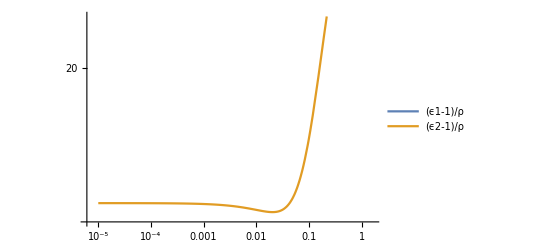

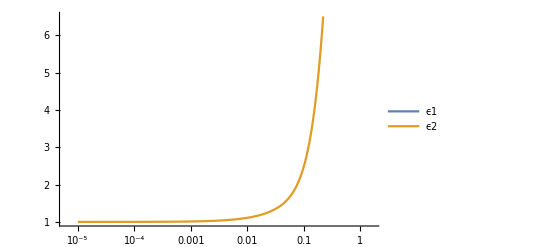

-Graphics-

```mathematica
T=400;
LogLogPlot[{(ϵ1-1)/ρ,(ϵ2-1)/ρ},{ρ,0.00001,1},PlotLegends->"Expressions"](*it shows second one is not so good*)
LogLinearPlot[{ϵ1,ϵ2},{ρ,0.00001,1},PlotLegends->"Expressions"]
LogLinearPlot[(ϵ1/ϵ2),{ρ,0.00001,1}]
```

## 238-873 up to 1000Mpa 1997

```mathematica
ClearAll["Global`*"]
```

### g

```mathematica
n=({{0.978224486826}, {-0.957771379375}, {0.237511794148}, {0.714692244396}, {-0.298217036956}, {-0.108863472196}, {0.949327488264*0.1}, {-0.980469816509*0.01}, {0.165167634970*10^-4}, {0.937359795772*10^-4}, {-0.123179218720*10^-9}, {0.196096504426*10^-2}});
```

```mathematica
i=({{1}, {1}, {1}, {2}, {3}, {3}, {4}, {5}, {6}, {7}, {10}});
```

```mathematica
j=({{0.25}, {1}, {2.5}, {1.5}, {1.5}, {2.5}, {2}, {2}, {5}, {0.5}, {10}});
```

```mathematica
-Graphics-;
-Graphics-;
```

```mathematica
Subscript[ρ, c]=322/Subscript[M, w];(*Subscript[ρ, c] for water is 0.322 g/cm^3*)
Subscript[T, c]=647.096;
```

```mathematica
g=1+ ∑_(h=1)^11 n[[h,1]](ρ/Subscript[ρ, c])^i[[h,1]] (Subscript[T, c]/T)^j[[h,1]]+n[[12,1]] (ρ/Subscript[ρ, c]) (T/228-1)^-1.2
```

1+(6.08995×10^-6 ρ M_w)/(-1+T/228)^1.2+0.0153223 (1/T)^0.25 ρ M_w+7856.9 (1/T)^2.5 ρ M_w-(1.92475 ρ M_w)/T+0.113465 (1/T)^1.5 ρ^2 M_w^2-0.000147034 (1/T)^1.5 ρ^3 M_w^3-0.0347325 (1/T)^2.5 ρ^3 M_w^3+(3.69769×10^-6 ρ^4 M_w^4)/T^2-(1.18602×10^-9 ρ^5 M_w^5)/T^2+(1.68125×10^-6 ρ^6 M_w^6)/T^5+6.64354×10^-21 (1/T)^0.5 ρ^7 M_w^7-(1.32332×10^-7 ρ^10 M_w^10)/T^10

### ϵ

```mathematica
-Graphics-;
```

```mathematica
Subscript[ϵ, 0]=(4*10^-7*Pi*299792458^2)^-1;
α=1.636*10^-40;
μ=6.138*10^-30;
k=1.380658*10^-23;
Subscript[N, A]=6.0221367*10^23;
Subscript[M, w]=0.018015268;
```

```mathematica
-Graphics-;
```

```mathematica
g
```

1+(1.09712×10^-7 ρ)/(-1+T/228)^1.2+0.000276036 (1/T)^0.25 ρ+141.544 (1/T)^2.5 ρ-(0.0346749 ρ)/T+0.0000368249 (1/T)^1.5 ρ^2-8.59686×10^-10 (1/T)^1.5 ρ^3-2.03076×10^-7 (1/T)^2.5 ρ^3+(3.89487×10^-13 ρ^4)/T^2-(2.25059×10^-18 ρ^5)/T^2+(5.74748×10^-17 ρ^6)/T^5+4.09152×10^-33 (1/T)^0.5 ρ^7-(4.76511×10^-25 ρ^10)/T^10

```mathematica
(*T=273;
ρ=1*1000/Subscript[M, w](*should be in mol/m^3 and 1g/cm^3=1000kg/m^3=1000/Subscript[M, w] mol/m^3*)*)
```

```mathematica
B=(Subscript[N, A] α)/(3 Subscript[ϵ, 0]) ρ
A=(Subscript[N, A] μ^2)/(Subscript[ϵ, 0] k)  (ρ g)/T
```

3.70906×10^-6 ρ

1/T 0.185596 ρ (1+(1.09712×10^-7 ρ)/(-1+T/228)^1.2+0.000276036 (1/T)^0.25 ρ+141.544 (1/T)^2.5 ρ-(0.0346749 ρ)/T+0.0000368249 (1/T)^1.5 ρ^2-8.59686×10^-10 (1/T)^1.5 ρ^3-2.03076×10^-7 (1/T)^2.5 ρ^3+(3.89487×10^-13 ρ^4)/T^2-(2.25059×10^-18 ρ^5)/T^2+(5.74748×10^-17 ρ^6)/T^5+4.09152×10^-33 (1/T)^0.5 ρ^7-(4.76511×10^-25 ρ^10)/T^10)

```mathematica
-Graphics-;
```

```mathematica
ϵ=(1+A+5B+√(9+2A+18B+A^2+10A B +9 B^2))/(4-4B);
```

```mathematica
ρ=x*1000/Subscript[M, w]
ϵ=(1+A+5B+√(9+2A+18B+A^2+10A B +9 B^2))/(4-4B)
```

55508.5 x

1/(4-0.823537 x)(1+1.02942 x+1/T 10302.2 x (1+(0.00608995 x)/(-1+T/228)^1.2+15.3223 (1/T)^0.25 x+7.8569×10^6 (1/T)^2.5 x-(1924.75 x)/T+113465. (1/T)^1.5 x^2-147034. (1/T)^1.5 x^3-3.47325×10^7 (1/T)^2.5 x^3+(3.69769×10^6 x^4)/T^2-(1.18602×10^6 x^5)/T^2+(1.68125×10^12 x^6)/T^5+6.64354 (1/T)^0.5 x^7-(1.32332×10^23 x^10)/T^10)+√(9+3.70592 x+0.381495 x^2+1/T 20604.3 x (1+(0.00608995 x)/(-1+T/228)^1.2+15.3223 (1/T)^0.25 x+7.8569×10^6 (1/T)^2.5 x-(1924.75 x)/T+113465. (1/T)^1.5 x^2-147034. (1/T)^1.5 x^3-3.47325×10^7 (1/T)^2.5 x^3+(3.69769×10^6 x^4)/T^2-(1.18602×10^6 x^5)/T^2+(1.68125×10^12 x^6)/T^5+6.64354 (1/T)^0.5 x^7-(1.32332×10^23 x^10)/T^10)+1/T 21210.6 x^2 (1+(0.00608995 x)/(-1+T/228)^1.2+15.3223 (1/T)^0.25 x+7.8569×10^6 (1/T)^2.5 x-(1924.75 x)/T+113465. (1/T)^1.5 x^2-147034. (1/T)^1.5 x^3-3.47325×10^7 (1/T)^2.5 x^3+(3.69769×10^6 x^4)/T^2-(1.18602×10^6 x^5)/T^2+(1.68125×10^12 x^6)/T^5+6.64354 (1/T)^0.5 x^7-(1.32332×10^23 x^10)/T^10)+1/T^2 1.06135×10^8 x^2 (1+(0.00608995 x)/(-1+T/228)^1.2+15.3223 (1/T)^0.25 x+7.8569×10^6 (1/T)^2.5 x-(1924.75 x)/T+113465. (1/T)^1.5 x^2-147034. (1/T)^1.5 x^3-3.47325×10^7 (1/T)^2.5 x^3+(3.69769×10^6 x^4)/T^2-(1.18602×10^6 x^5)/T^2+(1.68125×10^12 x^6)/T^5+6.64354 (1/T)^0.5 x^7-(1.32332×10^23 x^10)/T^10)^2))

## Simulation result

```mathematica
(*ClearAll["Global`*"]*)
```

### input

```mathematica
(*tRatio=1.2027236188031236;
pRatio=1/0.03342796387289012
N[%,30]*)
```

```mathematica
(*NumberForm[29.915073613292794,16]*)
```

```mathematica
(*tRatio*pRatio*)
```

```mathematica
(*NumberForm[0.0163624617374468397836596009546/35.97956559294134,16]*)
```

```mathematica
(*n=256;
ρ=1;
T=293.0;
AEE=-443.39693008792784;*)
```

```mathematica
(*ρ=1;
T=373;
AEE=-269.0199171623568;*)
```

```mathematica
(*p=ρ/pRatio;
t=T/tRatio;*)
```

### my method

```mathematica
(*(4 Pi)/3 1/n;
N[%,30]*)
```

```mathematica
(*ϵ1=1-(4 Pi)/3 p/n AEE t;
N[%,20]*)
```

### shu’s method it agree with my method

```mathematica
(*x=-AEE*t^2;
B=2(10^11-1)/(2*10^11+1);
d= (4 Pi)/9 p/(n t);*)
```

```mathematica
(*ϵ2=(1+2 d x+B d x)/(1-d x+B d x);
N[%,20]*)
```

## shu’s script

```mathematica
(*ClearAll["Global`*"]*)
```

```mathematica
(*Solve[(y-1)/(y+2)(1-(y-1)/(y+2) B)^-1==D x,y]*)
```

```mathematica
(*c=(4 Pi)/9 x/v/T;*)
```

```mathematica
(*A=c/(1+B c)*)
```

```mathematica
(*dc=(1+2A)/(1-A)//Simplify*)
```

```mathematica
(*1564860.5794890441/(540.4400394554818)^2*)
```

```mathematica
(*1-4/3*Pi*ρ/256*T*x*)
```

```mathematica
(*10/0.0300851674856011071*)
```

```mathematica
(**)
```

```mathematica
|
```

## Compare with three correlation

```mathematica
(*the ϵ3 density is in kg/mol but after I transfer to x it becomes g/cm^3 again!!!!*)
```

```mathematica
ClearAll["Global`*"]
```

### expressions

```mathematica
1/(4-0.8235371369683173 x)(1+1.0294214212103967 x+1/T 10302.172246903372 x (1+(0.006089953553602484 x)/(-1+T/228)^1.2+15.322330895079466 (1/T)^0.25 x+7.856897668412108*^6 (1/T)^2.5 x-(1924.7516413293324 x)/T+113464.60322878143 (1/T)^1.5 x^2-147034.04617955844 (1/T)^1.5 x^3-3.473252484583361*^7 (1/T)^2.5 x^3+(3.6976857532583666*^6 x^4)/T^2-(1.1860207863800817*^6 x^5)/T^2+(1.6812538671080532*^12 x^6)/T^5+6.6435403650343865 (1/T)^0.5 x^7-(1.3233230608637106*^23 x^10)/T^10)+√(9+3.705917116357428 x+0.38149504648085986 x^2+1/T 20604.344493806744 x (1+(0.006089953553602484 x)/(-1+T/228)^1.2+15.322330895079466 (1/T)^0.25 x+7.856897668412108*^6 (1/T)^2.5 x-(1924.7516413293324 x)/T+113464.60322878143 (1/T)^1.5 x^2-147034.04617955844 (1/T)^1.5 x^3-3.473252484583361*^7 (1/T)^2.5 x^3+(3.6976857532583666*^6 x^4)/T^2-(1.1860207863800817*^6 x^5)/T^2+(1.6812538671080532*^12 x^6)/T^5+6.6435403650343865 (1/T)^0.5 x^7-(1.3233230608637106*^23 x^10)/T^10)+1/T 21210.55359192315 x^2 (1+(0.006089953553602484 x)/(-1+T/228)^1.2+15.322330895079466 (1/T)^0.25 x+7.856897668412108*^6 (1/T)^2.5 x-(1924.7516413293324 x)/T+113464.60322878143 (1/T)^1.5 x^2-147034.04617955844 (1/T)^1.5 x^3-3.473252484583361*^7 (1/T)^2.5 x^3+(3.6976857532583666*^6 x^4)/T^2-(1.1860207863800817*^6 x^5)/T^2+(1.6812538671080532*^12 x^6)/T^5+6.6435403650343865 (1/T)^0.5 x^7-(1.3233230608637106*^23 x^10)/T^10)+1/T^2 1.0613475300486608*^8 x^2 (1+(0.006089953553602484 x)/(-1+T/228)^1.2+15.322330895079466 (1/T)^0.25 x+7.856897668412108*^6 (1/T)^2.5 x-(1924.7516413293324 x)/T+113464.60322878143 (1/T)^1.5 x^2-147034.04617955844 (1/T)^1.5 x^3-3.473252484583361*^7 (1/T)^2.5 x^3+(3.6976857532583666*^6 x^4)/T^2-(1.1860207863800817*^6 x^5)/T^2+(1.6812538671080532*^12 x^6)/T^5+6.6435403650343865 (1/T)^0.5 x^7-(1.3233230608637106*^23 x^10)/T^10)^2));
```

```mathematica
ϵ3=%/.(x->ρ)
```

1/(4-0.823537 ρ)(1+1.02942 ρ+1/T 10302.2 ρ (1+(0.00608995 ρ)/(-1+T/228)^1.2+15.3223 (1/T)^0.25 ρ+7.8569×10^6 (1/T)^2.5 ρ-(1924.75 ρ)/T+113465. (1/T)^1.5 ρ^2-147034. (1/T)^1.5 ρ^3-3.47325×10^7 (1/T)^2.5 ρ^3+(3.69769×10^6 ρ^4)/T^2-(1.18602×10^6 ρ^5)/T^2+(1.68125×10^12 ρ^6)/T^5+6.64354 (1/T)^0.5 ρ^7-(1.32332×10^23 ρ^10)/T^10)+√(9+3.70592 ρ+0.381495 ρ^2+1/T 20604.3 ρ (1+(0.00608995 ρ)/(-1+T/228)^1.2+15.3223 (1/T)^0.25 ρ+7.8569×10^6 (1/T)^2.5 ρ-(1924.75 ρ)/T+113465. (1/T)^1.5 ρ^2-147034. (1/T)^1.5 ρ^3-3.47325×10^7 (1/T)^2.5 ρ^3+(3.69769×10^6 ρ^4)/T^2-(1.18602×10^6 ρ^5)/T^2+(1.68125×10^12 ρ^6)/T^5+6.64354 (1/T)^0.5 ρ^7-(1.32332×10^23 ρ^10)/T^10)+1/T 21210.6 ρ^2 (1+(0.00608995 ρ)/(-1+T/228)^1.2+15.3223 (1/T)^0.25 ρ+7.8569×10^6 (1/T)^2.5 ρ-(1924.75 ρ)/T+113465. (1/T)^1.5 ρ^2-147034. (1/T)^1.5 ρ^3-3.47325×10^7 (1/T)^2.5 ρ^3+(3.69769×10^6 ρ^4)/T^2-(1.18602×10^6 ρ^5)/T^2+(1.68125×10^12 ρ^6)/T^5+6.64354 (1/T)^0.5 ρ^7-(1.32332×10^23 ρ^10)/T^10)+1/T^2 1.06135×10^8 ρ^2 (1+(0.00608995 ρ)/(-1+T/228)^1.2+15.3223 (1/T)^0.25 ρ+7.8569×10^6 (1/T)^2.5 ρ-(1924.75 ρ)/T+113465. (1/T)^1.5 ρ^2-147034. (1/T)^1.5 ρ^3-3.47325×10^7 (1/T)^2.5 ρ^3+(3.69769×10^6 ρ^4)/T^2-(1.18602×10^6 ρ^5)/T^2+(1.68125×10^12 ρ^6)/T^5+6.64354 (1/T)^0.5 ρ^7-(1.32332×10^23 ρ^10)/T^10)^2))

```mathematica
ϵ1=1+(4383.7996075295 ρ)/T+(-115.4445173+63460.116384395/T+0.06557809542176757 T) ρ^2+(-24836.93250237/T+0.10777259929565657 T-0.00007530476897770476 T^2) ρ^3+(-27.29401652-(3.3656845805654894*^6)/T^2+20534.662784549/T) ρ^4;
ϵ2=1+(4535.638 ρ)/T-(6.931894*^6 ρ^2)/T^2+(7.817505*^10 ρ^3)/T^3-(1.400863*^14 ρ^4)/T^4+(1.30838*^17 ρ^5)/T^5-(7.252169999999999*^19 ρ^6)/T^6+(2.464692*^22 ρ^7)/T^7-(5.041228*^24 ρ^8)/T^8+(5.6967440000000005*^26 ρ^9)/T^9-(2.732318*^28 ρ^10)/T^10;
```

### results

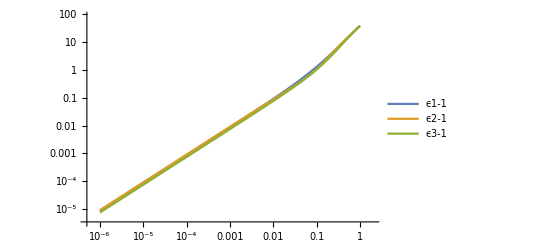

```mathematica
T=500;
LogLogPlot[{ϵ1-1,ϵ2-1,ϵ3-1},{ρ,0.000001,1},PlotLegends->"Expressions" ]
```

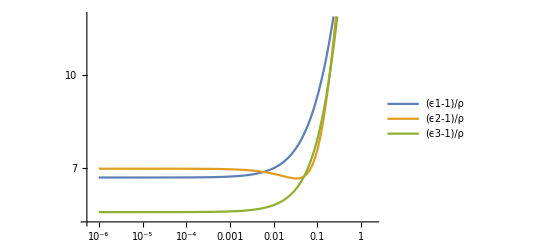

```mathematica
T=650;
LogLogPlot[{(ϵ1-1)/ρ,(ϵ2-1)/ρ,(ϵ3-1)/ρ},{ρ,0.000001,1},PlotLegends->"Expressions" ]
```

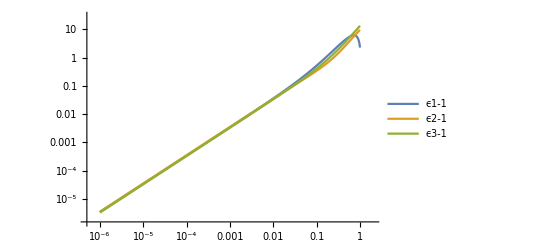

```mathematica
T=1300;
LogLogPlot[{ϵ1-1,ϵ2-1,ϵ3-1},{ρ,0.000001,1},PlotLegends->"Expressions" ]
```

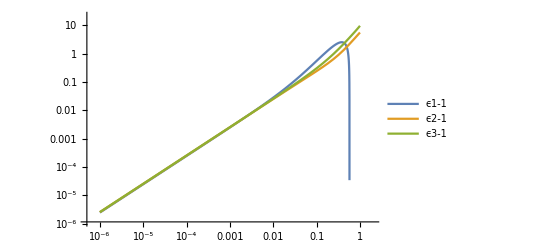

```mathematica
T=1800;
LogLogPlot[{ϵ1-1,ϵ2-1,ϵ3-1},{ρ,0.000001,1},PlotLegends->"Expressions" ]
```